Mathematica >

# EscapeProbability

EscapeProbability extends the capabilities of Mathematica to solve the radiative transfer problem (in the astronomical context) using the escape probability approximation.  It includes functions to numerically (iteratively) solve the involved equations of radiative transfer and statistical equilibrium. The relevant properties of the medium are taken from LAMBDA, the Leiden Atomic and Molecular Database (http://www.strw.leidenuniv.nl/~moldata/). The package includes functions to display the properties of many species, like energy levels, allowed transitions, collision rates and so on. This package has been inspired by the software RADEX (summarized in Van der Tak, F.F.S., Black, J.H., Schöier, F.L., Jansen, D.J., van Dishoeck, E.F. 2007, A&A 468, 627) which is an open source one-dimensional non-LTE radiative transfer code, that uses the escape probability formulation assuming an isothermal and homogeneous medium without large-scale velocity fields.  (http://www.strw.leidenuniv.nl/~moldata/radex.html)

This loads the package.

```mathematica
<<EscapeProbability`
```

## Radiative Transfer

The escape probability approximation is an approach to simplify the general radiative transfer problem and to decouple the radiative transfer equation from the statistical equations. The radiative transfer equation can be written as:

(d I_v)/(d s)=j_ν (r⃗)-I_ν( r⃗) α_ν

with the specific intensity of an object I_ν=dE/(dA dt dν dΩ θ cos) is defined as the energy that flows through the area element dA per time interval dt, per frequency interval dν  from the solid angle element dΩ (inclined against dA with the angle θ) at the point r⃗. Units of I_ν are for example [erg cm^-2 sec^-1 Hz^-1 sterad^-1]. α_ν is the absorption coefficient (in cm^-1) and can also be expressed as α_ν=n_i σ_ν where σ_ν is the absorption cross section in cm^2 and n_i the number density of the absorbing particles (in cm^-3).  j_ν is the emission coefficient. Hence, the above equation describes how the intensity changes along the line of sigh s by absorption and emission of photons. By defining the optical depth ⅆ τ_ν=α_ν(r⃗) ⅆs we can rewrite the radiative transfer equation

(d I_ν)/(d τ_ν)=S_ν(r⃗)+I_ν

where the source function S_ν=j_ν/α_ν. The formal solution to this equation is

I_ν (τ_ν)=∫_0^τ_ν S_ν ⅇ^(-(τ_ν-τ'_ν)) τ'_ν ⅆ τ'+0 I_ν ⅇ^τ_ν

### Interaction Radiation - Matter

To further specify τ_ν and S_ν let us take a look at possible interactions between photons and absorbing/emitting particles. Neglecting polarization, magnetic fields and dust continuum effects we find three processes:

absorption

spontaneous emission

induced emission

The probability for each of these processes is described by the Einstein coefficients B_12, A_21,and B_21 where 1 and 2 denote the lower and the upper energy level of an atom (or molecule). We A_21 as short hand for A_(2→1) indicating a transition from 2 to 1.

#### Absorption

An atom or molecule (from now on we will always use the term atom even if we mean molecule) residing in the lower energy state 1 (of a transition 1->2) can absorb a photon of the radiation field if the photon energy ⅇ_ν=hν corresponds to the energy difference of the two energy levels ⅇ_ν=ⅇ_2-ⅇ_1. The rate of this absorption is proportional to the intensity I_ν, the density of atoms in the state 1 n_1, a proportional factor describing the probability of the process B_12 and the profile function ϕ_ν describing the velocity distribution of the atoms in state 1

B_12 n_1 I_ν_12 ϕ_ν_12

This means the energy rate that is removed from the intensity field by absorption is

(B_12 n_1 I_ν_12 (h ν_12) ϕ_ν_12)/(4 π)

The 4π term is due to the assumption that the absorption is isotropic.

#### Spontaneous Emission

An atom in an excited energetic state 2 has a finite probability of undergoing a transition to the energetically lower state by spontaneously emitting a photon of energy hν_21=ⅇ_2-ⅇ_1. The probability for this decay is A_21 [s^-1] with its rate

A_12 n_2 ϕ_ν_21

This (isotropic) emissions provides an energy of

(A_12 n_2 (h ν_21) ϕ_ν_21)/(4 π)

to the radiation field.

#### Induced Emission

An atom in an excited energetic state 2 has also finite probability of undergoing a transition to the energetically lower state if a photon of energy hν_21=ⅇ_2-ⅇ_1 flies by. The probability for this induced decay is B_21 [cm^-2 erg^-1 s^-1] with the rate

B_21 n_2 I_ν_21 ϕ_ν_21

The line profile functions are normalized∫_(-∞)^(+∞) ϕ_a(⋁)ⅆν=d∫_(-∞)^(+∞) ϕ_e(⋁)ⅆν =1. Both profile functions could be different but for simplicity we make the assumption of complete redistribution which means that the frequency of an emitted photon is completely independent of the frequency of the prior absorption process. The atom has no "memory" of its past ϕ_e=ϕ_a=ϕ.

#### Einstein Relations

From the fact that the level populations (n_i) have to reach the Boltzmann distribution under thermodynamical equilibrium one can derive relations between the Einstein coefficients:

B_12 g_1=B_21 g_2

and

A_21=(B_21 (2 hν^3))/c^2

g_iis the statistical weight of the state i.

#### Source Function

Writing the absorption and emission coefficients in terms of the Einstein coefficients

j_ν=(A_21 hν n_2 ϕ)/(4 π) and α_ν=(hν (B_12 n_1-B_21 n_2))/(4 π)

allows us to rewrite the source functions

S_ν=A_21/(B_21 ((g_2 n_1)/(g_1 n_2)-1))

and we can define the excitation temperature which characterizes the ratio of n_1/n_2

n_2/n_1=(g_2 ϵ^(-hν/(k T_ex)))/g_1

and the source function becomes S_ν=B_ν(T_ex) with the black body radiation at temperature T_ex.

B_ν(T_ex)=(2 hν^3)/(c^2 ⅇ^(-hν/(k T_ex)-1))

#### Rayleigh Jeans Approximation

For h⋁≪kT, i.e. for small frequencies, the Rayleigh Jeans approximation is valid

B_ν(T)≃(2 hν^2)/c^2 kT

which means the intensity of the black body radiation is directly proportional to the temperature of the black body. For this reason it is common to express astronomically observed intensities in the radio (and submm) regime by giving so called brightness temperatures T_B. T_B is the temperature a black body must have in order to radiate the intensity I_ν at the frequency ν.

I_ν=(2 hν^2)/c^2 kT_B=(2k T_B)/λ^2 i.e.

I_ν(W/(Hz m^2 sr))=(3.08 (ν(MHz))^2 T_B(K))/10^28

Implicitly assuming Rayleigh Jeans we can rewrite the general solution of the radiative transfer equation for a homogeneous medium to

I_ν=B_ν T_ex (1-ⅇ^-τ_ν)+ⅈ_ν^bg ⅇ^-τ_ν leading to

T_R=T_bg ⅇ^-τ_ν+T_ex (1-ⅇ^-τ_ν)

which makes the Rayleigh Jeans approximation interesting for radio astronomy since one just thinks in terms of temperatures.

#### Statistical Equilibrium

With the radiative transfer equation given above one just has to specify the energy level populations n_i at all positions and the problem is solved. Unfortunately, this is far from simple because the I_ν at each position and n_i's at each position are coupled via the absorption and emission processes described above. To solve the problem at one spot one has to know the n_i at all other positions, which are dependent on the values of n_i at our chosen position. Numerically this is done via iterative numerical algorithms.

Assuming an I_νone has to solve the statistical equations to get the n_i which are then again used to calculate I_ν and so on. The statistical equations balance all populating and depopulating processes for each energy level. This includes collisions which haven't been considered so far.

The rate C_21 is the collision rate per second per molecule of the species of interest for the transition 2→1. The collisions follow the detailed balance equations

C_12 n_1=C_21 n_2

Using the Boltzmann distribution for n_1 and n_2 we can calculate

C_12=(C_21 g_2 ϵ^(-ΔE/(k T)))/g_1

Balancing all processes for a two level system one can write:

(ⅆ n_1)/ⅆt= -n_1(B_12 J̃ +C_12)+n_2(A_21+B_21 J̃+C_21)
(ⅆ n_2)/ⅆt= n_1(B_12 J̃ +C_12)-n_2(A_21+B_21 J̃+C_21)

with J̃=∫∫I_ν ⅆνⅆΩ .

## Escape Probability (EP)

One approach to reduce the complexity of the radiative transfer problem is to use approximations in order to decouple the radiative transfer equation from the statistical balance. We stated above that a photon that is emitted at a position r⃗ can be absorbed at another position  r⃗' and influence the level population there. Assuming an homogeneous, isothermal medium one can derive the probability of an  absorption while passing a column of absorber. This assumes that the medium along the flight path of the photon is in the same state as at position r⃗.  This is a strong assumption, but justified under certain conditions. For example, consider a outward expanding spherical shell. The atoms at outer radii have a velocity relative to the atoms at the center. This velocity difference produces a Doppler shift in frequency which makes an absorption in the expanding shell unlikely because the profile functions drops rapidly for shifted frequencies. This Doppler shift makes the expanding shell virtually transparent for photons emitted at the center and thus decouples the radiation from the matter in the shell. This particular approximation is called Sobolev approximation of LVG (large velocity gradient). The escape probability for a photon in an expanding shell is

β=(1-ⅇ^-τ)/τ

with the optical depth τ towards the observer.

Even without larger Doppler velocities one can derive probabilities for emitted photons to escape a cloud without being absorbed. This probability depends on the column density of material which the photon has to travel through. For a plane-parallel homogeneous slab of gas we find

β=(1-ⅇ^(-3 τ))/(3 τ)

For a uniform sphere one finds

β=(1.5 (ⅇ^-τ (2/τ^2+2/τ)-2/τ^2+1))/τ

For a turbulent medium one can estimate

β=1/(τ √(π ln(τ/2)))

If β is the probability for an emitted photon to leave the medium without further contributing to the level populations, the we can write J̃=S (1-β) which simplifies the statistical equations significantly, e.g.

(d n_1)/(d t)=C_12 n_1-C_21 n_2-n_2 βA_21

Since no J̃ radiation field occurs in the equation any more, they can be solved locally and then used to compute the radiation. We still have to iterate, because the new intensity influences the local level populations, but we are decoupled from the rest of the cloud!

EscapeProbabilityRun[s,N,Δv,n,T] | solve the radiative transfer problem for species s assuming column density N, FWHM line width Δv, density n and temperature T

EscapeProbability function to solve the radiative transfer problem using the EP approximation.

```mathematica
Style[EscapeProbabilityRun["p-h2o@lowT",1. 10^14,5,1 10^4,50.],9]
```

Number of Iterations:178

Line |  |  E_UP | Frequency |  Wavelength | T_EX | Tau | T_R | Flux | Flux
 |  | [K] | [GHz] | [µm] | [K] |  | [K] | [K km/s] | [erg/cm2/s]
1_1_1 | 0_0_0 | 53.4 | 1113.34 | 269.272 | 5.97154 | 8.58459 | 0.00694702 | 0.0369755 | 6.57147×10^-7
2_0_2 | 1_1_1 | 100.8 | 987.927 | 303.456 | 15.655 | 0.000802756 | 0.00193436 | 0.0102956 | 1.27846×10^-7
2_1_1 | 2_0_2 | 136.9 | 752.033 | 398.643 | 14.1856 | 0.000103192 | 0.000317381 | 0.00168926 | 9.2527×10^-9
2_2_0 | 2_1_1 | 195.9 | 1228.79 | 243.974 | 12.6718 | 5.29019×10^-6 | 3.00016×10^-6 | 0.0000159684 | 3.81552×10^-10

By default, the output is formatted as a table. To print the table contents as lists use the option TableOutput->False.

```mathematica
EscapeProbabilityRun["p-h2o@lowT",1. 10^14,5,1 10^4,50.,TableOutput->False]
```

Number of Iterations:178

{{1_1_1,0_0_0,53.4,1113.34,269.272,5.97154,8.58459,0.00694702,0.0369755,6.57147×10^-7},{2_0_2,1_1_1,100.8,987.927,303.456,15.655,0.000802756,0.00193436,0.0102956,1.27846×10^-7},{2_1_1,2_0_2,136.9,752.033,398.643,14.1856,0.000103192,0.000317381,0.00168926,9.2527×10^-9},{2_2_0,2_1_1,195.9,1228.79,243.974,12.6718,5.29019×10^-6,3.00016×10^-6,0.0000159684,3.81552×10^-10}}

The species has to be defined by pointing to the respective LAMBDA file. The package tries to find the correct file if only the name of a species is given, but be aware that for some species multiple LAMBDA files exists employing different assumptions for the given collision rates for instance.

```mathematica
Style[EscapeProbabilityRun["p-h2o@lowT",1. 10^14,5,1 10^4,50.],9]
```

Number of Iterations:178

Line |  |  E_UP | Frequency |  Wavelength | T_EX | Tau | T_R | Flux | Flux
 |  | [K] | [GHz] | [µm] | [K] |  | [K] | [K km/s] | [erg/cm2/s]
1_1_1 | 0_0_0 | 53.4 | 1113.34 | 269.272 | 5.97154 | 8.58459 | 0.00694702 | 0.0369755 | 6.57147×10^-7
2_0_2 | 1_1_1 | 100.8 | 987.927 | 303.456 | 15.655 | 0.000802756 | 0.00193436 | 0.0102956 | 1.27846×10^-7
2_1_1 | 2_0_2 | 136.9 | 752.033 | 398.643 | 14.1856 | 0.000103192 | 0.000317381 | 0.00168926 | 9.2527×10^-9
2_2_0 | 2_1_1 | 195.9 | 1228.79 | 243.974 | 12.6718 | 5.29019×10^-6 | 3.00016×10^-6 | 0.0000159684 | 3.81552×10^-10

"p-h2o@lowT" points to a data file for para-H_2 O with only the lowest transitions included, i.e. the ones that have sufficiently populated energy levels at low temperatures. The advantage is a short computation time. A more complete set of transitions of p-H_2 O takes longer to compute.

```mathematica
Style[EscapeProbabilityRun["p-h2o",1. 10^14,5,1 10^4,50.],9]
```

Number of Iterations:174

Line |  |  E_UP | Frequency |  Wavelength | T_EX | Tau | T_R | Flux | Flux
 |  | [K] | [GHz] | [µm] | [K] |  | [K] | [K km/s] | [erg/cm2/s]
1_1_1 | 0_0_0 | 53.4 | 1113.34 | 269.272 | 4.94312 | 8.58554 | 0.00107949 | 0.0057456 | 1.02114×10^-7
2_0_2 | 1_1_1 | 100.8 | 987.927 | 303.456 | 18.2472 | 0.00012136 | 0.000462444 | 0.00246136 | 3.0564×10^-8
2_1_1 | 2_0_2 | 136.9 | 752.033 | 398.643 | 5.57491 | 0.0000267219 | 1.48873×10^-6 | 7.92377×10^-6 | 4.34015×10^-11
2_2_0 | 2_1_1 | 195.9 | 1228.79 | 243.974 | 26.3932 | 2.2396×10^-8 | 1.5835×10^-7 | 8.42816×10^-7 | 2.01384×10^-11
3_1_3 | 2_2_0 | 204.7 | 183.31 | 1635.44 | -3.25141 | -3.02237×10^-9 | 2.95968×10^-8 | 1.57529×10^-7 | 1.24963×10^-14
3_2_2 | 3_1_3 | 296.8 | 1919.36 | 156.194 | 8.07035 | 4.13902×10^-8 | 4.20931×10^-11 | 2.24041×10^-10 | 2.04013×10^-14
3_3_1 | 4_0_4 | 410.4 | 1893.69 | 158.312 | 11.8161 | 1.39411×10^-12 | 5.78945×10^-14 | 3.08144×10^-13 | 2.69488×10^-17
4_2_2 | 3_3_1 | 454.3 | 916.172 | 327.223 | -14.945 | -4.39698×10^-13 | 2.04076×10^-11 | 1.0862×10^-10 | 1.07572×10^-15
4_1_3 | 4_0_4 | 396.4 | 1602.22 | 187.111 | 14.4767 | 6.73448×10^-10 | 2.56774×10^-10 | 1.36668×10^-9 | 7.23925×10^-14
4_2_2 | 4_1_3 | 454.3 | 1207.64 | 248.247 | -103.081 | -4.52189×10^-12 | 6.09379×10^-10 | 3.24342×10^-9 | 7.35658×10^-14
5_1_5 | 4_2_2 | 469.9 | 325.153 | 922.004 | 12.2043 | 1.84851×10^-13 | 1.10346×10^-12 | 5.87315×10^-12 | 2.60013×10^-18
5_2_4 | 4_3_1 | 598.8 | 970.315 | 308.964 | -27.7754 | -2.21531×10^-17 | 0. | 0. | 0.
5_3_3 | 4_4_0 | 725.1 | 474.689 | 631.555 | -7.92569 | -5.14915×10^-17 | 0. | 0. | 0.
5_3_3 | 6_0_6 | 725.1 | 1716.96 | 174.607 | 30.0435 | 1.10276×10^-16 | 6.29653×10^-16 | 3.35133×10^-15 | 2.18452×10^-19
6_3_3 | 5_4_2 | 951.8 | 1541.97 | 194.422 | -71.5121 | -2.16866×10^-22 | 0. | 0. | 0.
6_4_2 | 5_5_1 | 1090.3 | 470.889 | 636.652 | -7.94849 | -8.17481×10^-22 | 0. | 0. | 0.
6_2_4 | 6_1_5 | 867.3 | 1794.79 | 167.035 | -42.2574 | -1.17066×10^-17 | 0. | 0. | 0.
6_3_3 | 6_2_4 | 951.8 | 1762.04 | 170.139 | 10.6182 | 1.54822×10^-17 | 0. | 0. | 0.
6_2_4 | 7_1_7 | 867.3 | 488.491 | 613.711 | 9.30459 | 1.24326×10^-18 | 0. | 0. | 0.
7_2_6 | 6_3_3 | 1021. | 1440.78 | 208.076 | 14.0852 | 2.94098×10^-22 | 0. | 0. | 0.
7_3_5 | 6_4_2 | 1175.1 | 1766.2 | 169.739 | 80.8509 | 2.46256×10^-21 | 0. | 0. | 0.
7_4_4 | 6_5_1 | 1334.8 | 1172.53 | 255.681 | 19.2203 | 5.20725×10^-26 | 0. | 0. | 0.
7_5_3 | 6_6_0 | 1524.6 | 437.347 | 685.48 | 4.84087 | 5.27872×10^-25 | 0. | 0. | 0.
8_5_3 | 7_6_2 | 1807. | 1190.83 | 251.751 | 4.63721 | 2.52666×10^-26 | 0. | 0. | 0.
9_2_8 | 8_3_5 | 1554.5 | 906.206 | 330.822 | 28.2345 | 5.20998×10^-29 | 0. | 0. | 0.
9_4_6 | 10_1_9 | 1929.3 | 1435.01 | 208.913 | -688.12 | -2.05182×10^-33 | 0. | 0. | 0.
7_4_4 | 8_1_7 | 1334.8 | 1344.68 | 222.948 | 14.7542 | 3.48697×10^-26 | 0. | 0. | 0.
8_2_6 | 9_1_9 | 1414.2 | 1879.75 | 159.485 | 50.3117 | 6.67828×10^-25 | 0. | 0. | 0.

You can display the final escape probabilities for all transitions using the option ShowEscapeProbability→True.

```mathematica
EscapeProbabilityRun["p-h2o@lowT",1. 10^14,5,1 10^4,50.,ShowEscapeProbability->True]
```

Number of Iterations:178

{0.169998,0.999699,0.999961,0.999998}

In the above case the model cloud is virtually transparent for photons emitted in the last three transitions, while 83% of the photons emitted in the lowest transition are rather reabsorbed in the cloud than escaping it.

## Cloud Geometry

The probability for a photon to escape a model clouds depends on the geometry of the cloud. The standard geometry that is applied in EscapeProbability is a homogeneous spherical cloud.

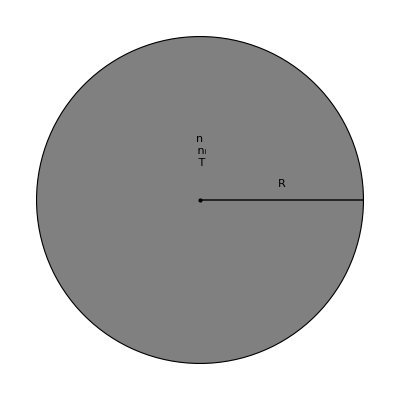

```mathematica
Graphics[{EdgeForm[{Thick,Black}],FaceForm[Gray],Disk[],PointSize[Large],Point[{0,0}],Thick,Line[{{0,0},{1,0}}],Style[Text["n\n n_i\n T",{0,0.3}],Italic],Style[Text["R",{0.5,0.1}],Italic]}]
```

The column density of the species under consideration is n×n_i×R. The advantage of the spherical geometry is the isotropy when sitting in the center. The escape probability is the same no matter in which direction.

Other geometries included are for instance a semi-infinite plane parallel slab of gas

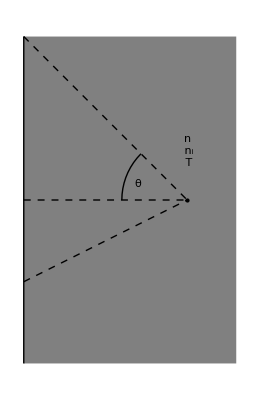

```mathematica
Graphics[{Gray,Rectangle[{0,-1},{ 1.3,1}],Black,Thick,Line[{{0,1},{0,-1}}],PointSize[Large],Point[{1,0}],Thin,Dashed,
Line[{{0,1},{1,0}}],Line[{{0,0},{1,0}}],Line[{{0,-0.5},{1,0}}],Dashing[{}],
Circle[{1,0},0.4,{3/4π,π}],
Style[Text["θ",{0.7,0.1}],Italic],
Style[Text["n\n n_i\n T",{1,0.3}],Italic]}
]
```

Here, the escape probability depends a function of the angle θ. Integrating over all angles (only the left half space, since the slab extends infinitely to the right) then gives the final β.

The choice of the model geometry changes the escape probability accordingly:

```mathematica
EscapeProbabilityRun["p-h2o@lowT",1. 10^14,5,1 10^4,50.,
Geometry->"Sphere",ShowEscapeProbability->True]
```

Number of Iterations:178

{0.169998,0.999699,0.999961,0.999998}

```mathematica
EscapeProbabilityRun["p-h2o@lowT",1. 10^14,5,1 10^4,50.,
Geometry->"PlaneParallel",ShowEscapeProbability->True]
```

Number of Iterations:780

{0.0388463,0.994558,0.999843,0.999992}

## Accessing the LAMBDA data files

The package offers a number of functions to display the contents of the used LAMBDA data files.

ShowCollisionPartners[species] | displays all collisional partners for which collision rates are listed in the data file
ShowCollisionRates[species] | displays the whole set of collision rates for each collision partner
ShowCollisionTemperatures[species] | displays the temperature grid for which collision rates are given
ShowEnergyLevels[species] | displays the energy levels of species together with properties of these levels
ShowTransitions[species] | displays all listed transition of species with their properties

Functions in EscapeProbability that provide direct access to the LAMBDA database files..

LAMBDA lists the energy levels of a species in the following order:
Level, Energies(cm^-1), statistical weight, J of lower level (or set of quantum number if not linear rotator)

```mathematica
TableForm[ShowEnergyLevels["CO"][[1;;10]],TableHeadings->{None,{"Nr.","E[cm^-1]","g","J_lower"}}]
```

Nr. | E[cm^-1] | g | J_lower
1 | 0. | 1. | 0
2 | 3.84503 | 3. | 1
3 | 11.5349 | 5. | 2
4 | 23.0695 | 7. | 3
5 | 38.4482 | 9. | 4
6 | 57.6703 | 11. | 5
7 | 80.7355 | 13. | 6
8 | 107.642 | 15. | 7
9 | 138.39 | 17. | 8
10 | 172.978 | 19. | 9

Transitions have the following entries:

Transition number, upper level number, lower level number, Einstein A value, frequency [GHz], and E_u[K].

```mathematica
TableForm[ShowTransitions["CO"][[1;;10]],TableHeadings->{None,{"Nr.","upper","lower","A_ul[s^-1]","ν [GHz]","E_u[K]"}}]
```

Nr. | upper | lower | A_ul[s^-1] | ν [GHz] | E_u[K]
1 | 2 | 1 | 7.203×10^-8 | 115.271 | 5.53
2 | 3 | 2 | 6.91×10^-7 | 230.538 | 16.6
3 | 4 | 3 | 2.497×10^-6 | 345.796 | 33.19
4 | 5 | 4 | 6.126×10^-6 | 461.041 | 55.32
5 | 6 | 5 | 0.00001221 | 576.268 | 82.97
6 | 7 | 6 | 0.00002137 | 691.473 | 116.16
7 | 8 | 7 | 0.00003422 | 806.652 | 154.87
8 | 9 | 8 | 0.00005134 | 921.8 | 199.11
9 | 10 | 9 | 0.0000733 | 1036.91 | 248.88
10 | 11 | 10 | 0.0001006 | 1151.99 | 304.16

The collision partners for which collision rates are present can be listed by ShowCollisionPartners

```mathematica
ShowCollisionPartners["CO"]//TableForm
```

ShowCollisionPartners::combop: If ortho- and para-H2 is given seperately as collision partners   the default behavior is to combine both into a single collision partner. In that case only one   H2 density needs to be given.

2 | CO-pH2 | from | Yang | et | al. | (2010)
3 | CO-oH2 | from | Yang | et | al. | (2010).

A warning is displayed to indicate that separate collision rates for para- and ortho H_2 are listed which are usually combined into a single collision rate.

The number of collision partners varies across the different species. Collision rates are difficult to measure and to calculate.

```mathematica
ShowCollisionPartners["hco+@xpol.dat"]//TableForm
```

1 | HCO+ | - | H2 | from | Flower | (1999) | + | extrapolation

```mathematica
ShowCollisionPartners["co.dat"]//TableForm
```

ShowCollisionPartners::combop: If ortho- and para-H2 is given seperately as collision partners   the default behavior is to combine both into a single collision partner. In that case only one   H2 density needs to be given.

2 | CO-pH2 | from | Yang | et | al. | (2010)
3 | CO-oH2 | from | Yang | et | al. | (2010).

```mathematica
ShowCollisionPartners["catom.dat"]//TableForm
```

ShowCollisionPartners::combop: If ortho- and para-H2 is given seperately as collision partners   the default behavior is to combine both into a single collision partner. In that case only one   H2 density needs to be given.

5 | C | + | H | ! | Launay | & | Roueff | 1977 |  |  |  |  |  | 
4 | C | + | e | ! | from | Johnson, | Burke, | & | Kingston | 1987, | JPhysB, | 20, | 2553 | 
7 | C | + | H+ | ! | Roueff | & | Le | Bourlot | 1990, | A&A, | 236, | 515 |  | 
6 | C | + | He | ! | Staemmler, | V., | Flower, | D.R. | 1991, | J. | Phys. | B, | 24, | 2343
2 | C | + | p-H2 | ! | K. | Schroeder | et | al. | 1991, | J. | Phys. | B, | 24, | 2487
3 | C | + | o-H2 | ! | K. | Schroeder | et | al. | 1991, | J. | Phys. | B, | 24, | 2487

```mathematica
ShowCollisionPartners["c+.dat"]//TableForm
```

ShowCollisionPartners::combop: If ortho- and para-H2 is given seperately as collision partners   the default behavior is to combine both into a single collision partner. In that case only one   H2 density needs to be given.

2 | C+ | + | pH2 | ! | Flower | & | Launay | (1977, | JPB, | 10, | 3673); | no | corr. | for | Flower | (1988)
3 | C+ | + | oH2 | ! | Flower | & | Launay | (1977, | JPB, | 10, | 3673) |  |  |  |  | 
5 | C+ | + | H | ! | Launay | & | Roueff, | 1977, | JPB, | 10, | 879 |  |  |  |  | 
4 | C+ | + | e | ! | Wilson | & | Bell, | 2002, | MNRAS, | 337, | 1027 |  |  |  |  |

The collision rates in the LAMBDA database are provided for a set of temperatures for which the rates have been measured or calculated. EscapeProbabilityRun interpolates the collision rates on their provided temperature grid. You can show the temperature grid of the collision rates.

```mathematica
ShowCollisionTemperatures["co.dat"]
```

{2.,5.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,150.,200.,300.,400.,500.,600.,700.,750.,800.,900.,1000.,2000.,3000.}

```mathematica
ShowCollisionTemperatures["co.dat"]//Length
```

25

In the case of CO this means, for each transition the data files contain 25 collision rate coefficients.

You can also display all collision rates that are given in the LAMBDA files.

```mathematica
TableForm[ShowCollisionRates["o-h2o@lowT.dat"],TableHeadings->{None,Join[{"Nr.","upper","lower"},#<>" K"&/@ToString/@ShowCollisionTemperatures["o-h2o@lowT.dat"]]}]
```

Nr. | upper | lower | 5. K | 8. K | 12. K | 16. K | 20. K | 40. K | 60. K | 80. K | 100. K | 120. K | 140. K
1 | 2 | 1 | 2.19788×10^-10 | 2.29782×10^-10 | 2.49766×10^-10 | 2.59758×10^-10 | 2.69553×10^-10 | 2.5917×10^-10 | 1.9671×10^-10 | 1.51581×10^-10 | 1.24912×10^-10 | 1.09871×10^-10 | 1.00985×10^-10
2 | 3 | 1 | 7.69431×10^-11 | 8.19391×10^-11 | 8.89321×10^-11 | 9.49261×10^-11 | 9.88609×10^-11 | 1.00098×10^-10 | 8.62642×10^-11 | 6.99007×10^-11 | 6.48338×10^-11 | 5.87702×10^-11 | 5.58478×10^-11
3 | 3 | 2 | 8.49311×10^-11 | 8.99271×10^-11 | 9.49231×10^-11 | 9.89191×10^-11 | 9.98538×10^-11 | 8.8886×10^-11 | 6.78048×10^-11 | 5.22634×10^-11 | 4.2694×10^-11 | 3.7372×10^-11 | 3.35652×10^-11
4 | 4 | 1 | 1.99836×10^-11 | 2.09829×10^-11 | 2.09831×10^-11 | 2.19823×10^-11 | 2.19686×10^-11 | 2.09297×10^-11 | 1.80463×10^-11 | 1.51021×10^-11 | 1.34082×10^-11 | 1.24527×10^-11 | 1.19159×10^-11
5 | 4 | 2 | 4.7972×10^-11 | 4.9971×10^-11 | 5.1969×10^-11 | 5.2968×10^-11 | 5.39412×10^-11 | 5.47243×10^-11 | 4.85418×10^-11 | 4.32745×10^-11 | 4.00716×10^-11 | 3.91794×10^-11 | 3.82858×10^-11
6 | 4 | 3 | 6.69431×10^-11 | 7.29371×10^-11 | 7.79321×10^-11 | 8.2927×10^-11 | 8.48661×10^-11 | 7.99536×10^-11 | 6.34278×10^-11 | 4.94414×10^-11 | 4.11083×10^-11 | 3.6523×10^-11 | 3.35684×10^-11
7 | 5 | 1 | 1.8989×10^-11 | 1.89893×10^-11 | 1.89895×10^-11 | 1.89897×10^-11 | 1.998×10^-11 | 1.69648×10^-11 | 1.61789×10^-11 | 1.48021×10^-11 | 1.40559×10^-11 | 1.34387×10^-11 | 1.34038×10^-11
8 | 5 | 2 | 1.79857×10^-11 | 1.79858×10^-11 | 1.69868×10^-11 | 1.69867×10^-11 | 1.69763×10^-11 | 1.4616×10^-11 | 1.17658×10^-11 | 9.7505×10^-12 | 8.23513×10^-12 | 7.67155×10^-12 | 7.43938×10^-12
9 | 5 | 3 | 6.995×10^-11 | 7.39461×10^-11 | 7.89411×10^-11 | 8.29371×10^-11 | 8.68806×10^-11 | 8.57862×10^-11 | 7.2149×10^-11 | 5.91975×10^-11 | 5.15908×10^-11 | 4.72626×10^-11 | 4.47493×10^-11
10 | 5 | 4 | 2.89728×10^-11 | 3.19701×10^-11 | 3.59664×10^-11 | 3.79645×10^-11 | 3.89349×10^-11 | 3.12982×10^-11 | 2.16383×10^-11 | 1.5435×10^-11 | 1.16774×10^-11 | 9.35689×10^-12 | 8.0613×10^-12

You can switch of the combining of ortho- and para rates using the option CombineOrthoPara->False. As a result, you get separate collision rates displayed for o/p-H_2.

```mathematica
ShowCollisionPartners["o-h2o@lowT.dat"] // TableForm
```

ShowCollisionPartners::combop: If ortho- and para-H2 is given seperately as collision partners   the default behavior is to combine both into a single collision partner. In that case only one   H2 density needs to be given.

2 | oH2O | - | pH2 | from | Dubernet | & | Grosjean | (2002) | and | Phillips | et | al. | (1996) | for | T>20K
3 | oH2O | - | oH2 | from | Grosjean | et | al. | (2003) | and | Phillips | et | al. | (1996) | for | T>20K

here the rates for para-H_2

```mathematica
TableForm[First@ShowCollisionRates["o-h2o@lowT.dat",CombineOrthoPara -> False],TableHeadings->{None,Join[{"Nr.","upper","lower"},#<>" K"&/@ToString/@First@ShowCollisionTemperatures["o-h2o@lowT.dat",CombineOrthoPara -> False]]}]
```

Nr. | upper | lower | 5. K | 8. K | 12. K | 16. K | 20. K | 40. K | 60. K | 80. K | 100. K | 120. K | 140. K
1 | 2 | 1 | 8.2×10^-12 | 1.2×10^-11 | 1.6×10^-11 | 1.8×10^-11 | 1.9×10^-11 | 1.6×10^-11 | 1.9×10^-11 | 2.2×10^-11 | 2.4×10^-11 | 2.7×10^-11 | 3.×10^-11
2 | 3 | 1 | 2.×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.2×10^-11 | 2.2×10^-11 | 2.3×10^-11 | 2.5×10^-11 | 2.6×10^-11 | 2.8×10^-11
3 | 3 | 2 | 1.6×10^-11 | 1.7×10^-11 | 1.8×10^-11 | 1.8×10^-11 | 1.8×10^-11 | 1.7×10^-11 | 1.6×10^-11 | 1.6×10^-11 | 1.5×10^-11 | 1.5×10^-11 | 1.5×10^-11
4 | 4 | 1 | 3.6×10^-12 | 3.9×10^-12 | 4.1×10^-12 | 4.3×10^-12 | 4.4×10^-12 | 4.6×10^-12 | 4.8×10^-12 | 4.9×10^-12 | 5.1×10^-12 | 5.3×10^-12 | 5.5×10^-12
5 | 4 | 2 | 2.×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.2×10^-11 | 2.3×10^-11 | 2.5×10^-11 | 2.6×10^-11
6 | 4 | 3 | 1.×10^-11 | 1.×10^-11 | 1.×10^-11 | 9.9×10^-12 | 9.9×10^-12 | 8.6×10^-12 | 9.×10^-12 | 9.6×10^-12 | 1.×10^-11 | 1.1×10^-11 | 1.2×10^-11
7 | 5 | 1 | 8.×10^-12 | 8.3×10^-12 | 8.5×10^-12 | 8.7×10^-12 | 8.8×10^-12 | 8.8×10^-12 | 8.9×10^-12 | 9.×10^-12 | 9.2×10^-12 | 9.5×10^-12 | 9.8×10^-12
8 | 5 | 2 | 3.7×10^-12 | 3.8×10^-12 | 3.8×10^-12 | 3.7×10^-12 | 3.7×10^-12 | 3.7×10^-12 | 3.7×10^-12 | 3.9×10^-12 | 4.1×10^-12 | 4.3×10^-12 | 4.6×10^-12
9 | 5 | 3 | 2.×10^-11 | 2.×10^-11 | 2.×10^-11 | 2.×10^-11 | 2.×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.2×10^-11 | 2.3×10^-11 | 2.4×10^-11
10 | 5 | 4 | 1.8×10^-12 | 2.1×10^-12 | 2.4×10^-12 | 2.5×10^-12 | 2.5×10^-12 | 2.1×10^-12 | 1.9×10^-12 | 1.8×10^-12 | 1.7×10^-12 | 1.7×10^-12 | 1.7×10^-12

and these are for ortho-H_2

```mathematica
TableForm[Last@ShowCollisionRates["o-h2o@lowT.dat",CombineOrthoPara -> False],TableHeadings->{None,Join[{"Nr.","upper","lower"},#<>" K"&/@ToString/@Last@ShowCollisionTemperatures["o-h2o@lowT.dat",CombineOrthoPara -> False]]}]
```

Nr. | upper | lower | 5. K | 8. K | 12. K | 16. K | 20. K | 40. K | 60. K | 80. K | 100. K | 120. K | 140. K
1 | 2 | 1 | 2.2×10^-10 | 2.3×10^-10 | 2.5×10^-10 | 2.6×10^-10 | 2.7×10^-10 | 2.9×10^-10 | 2.9×10^-10 | 2.9×10^-10 | 2.9×10^-10 | 2.9×10^-10 | 2.9×10^-10
2 | 3 | 1 | 7.7×10^-11 | 8.2×10^-11 | 8.9×10^-11 | 9.5×10^-11 | 9.9×10^-11 | 1.1×10^-10 | 1.2×10^-10 | 1.2×10^-10 | 1.3×10^-10 | 1.3×10^-10 | 1.3×10^-10
3 | 3 | 2 | 8.5×10^-11 | 9.×10^-11 | 9.5×10^-11 | 9.9×10^-11 | 1.×10^-10 | 9.8×10^-11 | 9.5×10^-11 | 9.1×10^-11 | 8.8×10^-11 | 8.6×10^-11 | 8.3×10^-11
4 | 4 | 1 | 2.×10^-11 | 2.1×10^-11 | 2.1×10^-11 | 2.2×10^-11 | 2.2×10^-11 | 2.3×10^-11 | 2.5×10^-11 | 2.6×10^-11 | 2.7×10^-11 | 2.8×10^-11 | 2.9×10^-11
5 | 4 | 2 | 4.8×10^-11 | 5.×10^-11 | 5.2×10^-11 | 5.3×10^-11 | 5.4×10^-11 | 5.9×10^-11 | 6.3×10^-11 | 6.6×10^-11 | 6.8×10^-11 | 7.×10^-11 | 7.1×10^-11
6 | 4 | 3 | 6.7×10^-11 | 7.3×10^-11 | 7.8×10^-11 | 8.3×10^-11 | 8.5×10^-11 | 8.9×10^-11 | 9.2×10^-11 | 9.2×10^-11 | 9.2×10^-11 | 9.2×10^-11 | 9.1×10^-11
7 | 5 | 1 | 1.9×10^-11 | 1.9×10^-11 | 1.9×10^-11 | 1.9×10^-11 | 2.×10^-11 | 1.8×10^-11 | 2.×10^-11 | 2.1×10^-11 | 2.2×10^-11 | 2.2×10^-11 | 2.3×10^-11
8 | 5 | 2 | 1.8×10^-11 | 1.8×10^-11 | 1.7×10^-11 | 1.7×10^-11 | 1.7×10^-11 | 1.6×10^-11 | 1.6×10^-11 | 1.6×10^-11 | 1.5×10^-11 | 1.5×10^-11 | 1.5×10^-11
9 | 5 | 3 | 7.×10^-11 | 7.4×10^-11 | 7.9×10^-11 | 8.3×10^-11 | 8.7×10^-11 | 9.4×10^-11 | 9.9×10^-11 | 1.×10^-10 | 1.×10^-10 | 1.×10^-10 | 1.×10^-10
10 | 5 | 4 | 2.9×10^-11 | 3.2×10^-11 | 3.6×10^-11 | 3.8×10^-11 | 3.9×10^-11 | 3.5×10^-11 | 3.2×10^-11 | 3.×10^-11 | 2.8×10^-11 | 2.6×10^-11 | 2.5×10^-11

When collision rate coefficients for more than one partners are listed, they not necessarily have identical temperature grid points, nor do they cover the same temperature ranges or apply to all listed transitions.

```mathematica
Riffle[
Style[#,Red,Bold]&/@ShowCollisionPartners["c+.dat"][[All, 2 ;; 4]]// Quiet, Table[TableForm[ShowCollisionRates["c+.dat", CombineOrthoPara -> False][[i]], TableHeadings -> {None, Join[{"Nr.", "upper", "lower"}, # <> " K" & /@ ToString /@ ShowCollisionTemperatures["c+.dat", CombineOrthoPara -> False][[i]]]}], {i, 1, Length@ShowCollisionRates["c+.dat", CombineOrthoPara -> False]}]] // Column
```

{C+,+,pH2}
Nr. | upper | lower | 10. K | 20. K | 50. K | 100. K | 200. K | 250. K
1 | 2 | 1 | 3.×10^-10 | 3.4×10^-10 | 3.9×10^-10 | 4.3×10^-10 | 4.6×10^-10 | 4.7×10^-10
{C+,+,oH2}
Nr. | upper | lower | 10. K | 20. K | 50. K | 100. K | 200. K | 250. K
1 | 2 | 1 | 4.4×10^-10 | 4.6×10^-10 | 4.9×10^-10 | 5.1×10^-10 | 5.6×10^-10 | 5.7×10^-10
{C+,+,H}
Nr. | upper | lower | 5. K | 10. K | 20. K | 50. K | 100. K | 200. K | 300. K | 500. K | 1000. K | 3162. K
1 | 2 | 1 | 5.9×10^-10 | 6.5×10^-10 | 7.×10^-10 | 7.7×10^-10 | 8.1×10^-10 | 8.3×10^-10 | 8.5×10^-10 | 8.9×10^-10 | 9.8×10^-10 | 1.1×10^-9
{C+,+,e}
Nr. | upper | lower | 10. K | 20. K | 50. K | 100. K | 316.2 K | 1000. K | 2000. K | 10000. K | 20000. K
1 | 2 | 1 | 1.2×10^-6 | 8.4×10^-7 | 5.3×10^-7 | 3.8×10^-7 | 2.1×10^-7 | 1.2×10^-7 | 8.6×10^-8 | 4.8×10^-8 | 3.7×10^-8
2 | 3 | 1 | 4.×10^-7 | 2.8×10^-7 | 1.8×10^-7 | 1.3×10^-7 | 7.1×10^-8 | 4.×10^-8 | 2.8×10^-8 | 1.2×10^-8 | 8.5×10^-9
3 | 4 | 1 | 2.9×10^-7 | 2.1×10^-7 | 1.3×10^-7 | 9.3×10^-8 | 5.2×10^-8 | 2.9×10^-8 | 2.1×10^-8 | 9.×10^-9 | 6.3×10^-9
4 | 5 | 1 | 1.2×10^-7 | 8.5×10^-8 | 5.3×10^-8 | 3.8×10^-8 | 2.1×10^-8 | 1.2×10^-8 | 8.5×10^-9 | 3.8×10^-9 | 2.7×10^-9
5 | 3 | 2 | 2.7×10^-7 | 1.9×10^-7 | 1.2×10^-7 | 8.6×10^-8 | 4.9×10^-8 | 2.7×10^-8 | 1.9×10^-8 | 8.7×10^-9 | 6.1×10^-9
6 | 4 | 2 | 3.8×10^-7 | 2.7×10^-7 | 1.7×10^-7 | 1.2×10^-7 | 6.7×10^-8 | 3.8×10^-8 | 2.7×10^-8 | 1.2×10^-8 | 8.3×10^-9
7 | 5 | 2 | 5.5×10^-7 | 3.9×10^-7 | 2.5×10^-7 | 1.7×10^-7 | 9.8×10^-8 | 5.5×10^-8 | 3.9×10^-8 | 1.7×10^-8 | 1.2×10^-8

MORE ABOUT

Escape Probability